```mathematica
Subscript[Ψ, nlm][r_,θ_,φ_]=ⅇ^(-r/n) √(((2/n)^3 (-l+n-1)!)/(2 n (l+n)!)) ((2 r)/n)^l LaguerreL[-l+n-1,2 l+1,(2 r)/n] SphericalHarmonicY[l,m,θ,φ]
```

2^(1+l) ⅇ^(-r/n) (r/n)^l √(((-1-l+n)!)/(n^4 (l+n)!)) LaguerreL[-1-l+n,1+2 l,(2 r)/n] SphericalHarmonicY[l,m,θ,φ]

```mathematica
Subscript[n, ex(28)][r_]=Integrate[2*Sin[θ]Sum[Abs[Subscript[Ψ, nlm][r,θ,φ]]^2,{n,1,3},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]
```

1/78732 ⅇ^(-2 Re[r]) (629856+19683 ⅇ^Re[r] Abs[2-r]^2+13122 ⅇ^Re[r] Abs[r]^2+2304 ⅇ^((4 Re[r])/3) Abs[r]^2+64 ⅇ^((4 Re[r])/3) Abs[r]^4+128 ⅇ^((4 Re[r])/3) Abs[(-6+r) r]^2+32 ⅇ^((4 Re[r])/3) Abs[27-18 r+2 r^2]^2+6561 ⅇ^Re[r] r Conjugate[r]+64 ⅇ^((4 Re[r])/3) Abs[r]^2 Im[r]^2-768 ⅇ^((4 Re[r])/3) Abs[r]^2 Re[r]+64 ⅇ^((4 Re[r])/3) Abs[r]^2 Re[r]^2)

```mathematica
Subscript[n, ex(10)][r_]=Integrate[2*Sin[θ]Sum[Abs[Subscript[Ψ, nlm][r,θ,φ]]^2,{n,1,2},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]
```

-1/2 ⅇ^(-2 Re[r]) (-16-2 ⅇ^Re[r]-ⅇ^Re[r] Abs[r]^2+2 ⅇ^Re[r] Re[r])

```mathematica
Subscript[n, ex(2)][r_]=Integrate[2*Sin[θ]Sum[Abs[Subscript[Ψ, nlm][r,θ,φ]]^2,{n,1,1},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]
```

8 ⅇ^(-2 Re[r])

```mathematica
Subscript[S, n][z_]=n(LaguerreL[n-1,1,z])^2+n (LaguerreL[n-2,1,z])^2+(z-2n)LaguerreL[n-1,1,z]LaguerreL[n-2,1,z]
```

n LaguerreL[-2+n,1,z]^2+(-2 n+z) LaguerreL[-2+n,1,z] LaguerreL[-1+n,1,z]+n LaguerreL[-1+n,1,z]^2

```mathematica
Subscript[ρ, 28][r_]=Sum[n^-4 E^(-2r/n)(n LaguerreL[-2+n,1,2r/n]^2+(-2 n+2r/n) LaguerreL[-2+n,1,2r/n] LaguerreL[-1+n,1,2r/n]+n LaguerreL[-1+n,1,2r/n]^2),{n,1,3}]/Pi
```

1/π(1/16 ⅇ^-r (2+2 (2-r)^2+(2-r) (-4+r))+1/81 ⅇ^(-2 r/3) (3 (2-(2 r)/3)^2+1/9 (2-(2 r)/3) (-6+(2 r)/3) (27-18 r+2 r^2)+1/27 (27-18 r+2 r^2)^2)+ⅇ^(-2 r) (1+(-2+2 r) LaguerreL[-1,1,2 r]+LaguerreL[-1,1,2 r]^2))

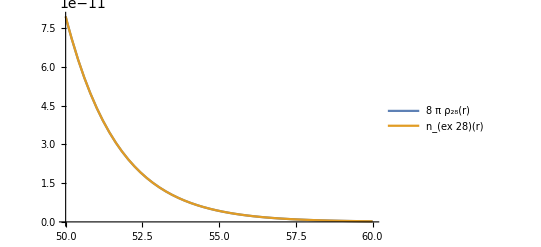

```mathematica
Plot[{8Pi Subscript[ρ, 28][r],Subscript[n, ex(28)][r]},{r,50,60},PlotLegends->"Expressions"]
```

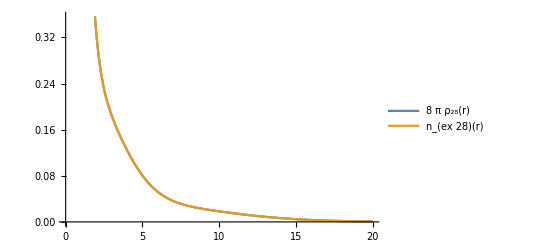

```mathematica
Plot[{8Pi Subscript[ρ, 28][r],Subscript[n, ex(28)][r]},{r,0,20},PlotLegends->"Expressions"]
```

```mathematica
Limit[8Pi Subscript[ρ, 28][r]/Subscript[n, ex(28)][r],r->Infinity]
```

1

```mathematica
Subscript[ρ, 10][r_]=Sum[n^-4 E^(-2r/n)(n LaguerreL[-2+n,1,2r/n]^2+(-2 n+2r/n) LaguerreL[-2+n,1,2r/n] LaguerreL[-1+n,1,2r/n]+n LaguerreL[-1+n,1,2r/n]^2),{n,1,2}]/Pi
```

(1/16 ⅇ^-r (2+2 (2-r)^2+(2-r) (-4+r))+ⅇ^(-2 r) (1+(-2+2 r) LaguerreL[-1,1,2 r]+LaguerreL[-1,1,2 r]^2))/π

```mathematica
Subscript[ρ, 10](r_)=(∑_(n=1)^2 (ⅇ^(-(2 r)/n) (n (n-21(2 r)/n)^2+((2 r)/n-2 n) n-11(2 r)/n n-21(2 r)/n+n (n-11(2 r)/n)^2))/n^4)/π
```

```mathematica
Subscript[ρ, 2][r_]=Sum[n^-4 E^(-2r/n)(n LaguerreL[-2+n,1,2r/n]^2+(-2 n+2r/n) LaguerreL[-2+n,1,2r/n] LaguerreL[-1+n,1,2r/n]+n LaguerreL[-1+n,1,2r/n]^2),{n,1,1}]/Pi
```

(ⅇ^(-2 r) (1+(-2+2 r) LaguerreL[-1,1,2 r]+LaguerreL[-1,1,2 r]^2))/π

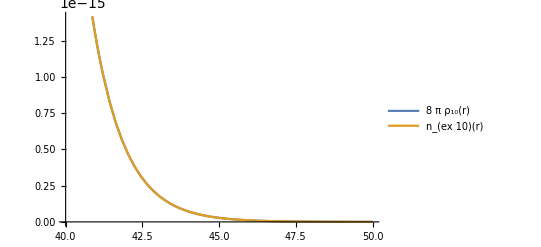

```mathematica
Plot[{8Pi Subscript[ρ, 10][r],Subscript[n, ex(10)][r]},{r,40,50},PlotLegends->"Expressions"]
```

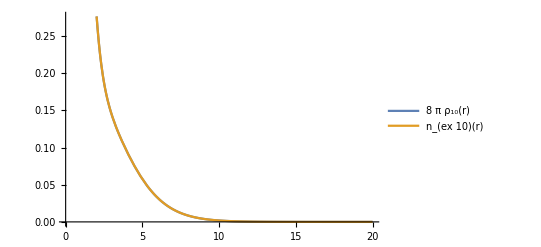

```mathematica
Plot[{8Pi Subscript[ρ, 10][r],Subscript[n, ex(10)][r]},{r,0,20},PlotLegends->"Expressions"]
```

```mathematica
Limit[8Pi Subscript[ρ, 10][r]/Subscript[n, ex(10)][r],r->Infinity]
```

1

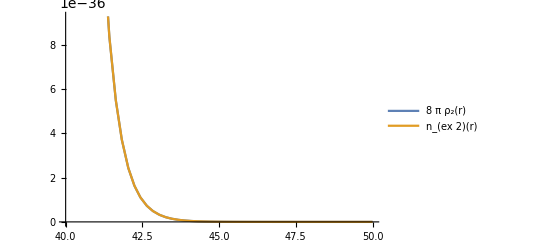

```mathematica
Plot[{8Pi Subscript[ρ, 2][r],Subscript[n, ex(2)][r]},{r,40,50},PlotLegends->"Expressions"]
```

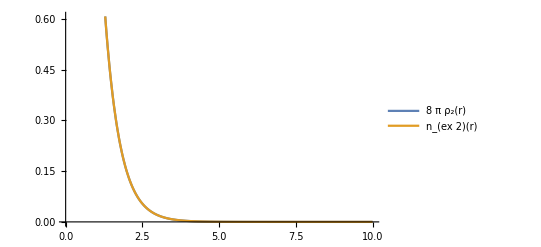

```mathematica
Plot[{8Pi Subscript[ρ, 2][r],Subscript[n, ex(2)][r]},{r,0,10},PlotLegends->"Expressions"]
```

```mathematica
Limit[8Pi Subscript[ρ, 2][r]/Subscript[n, ex(2)][r],r->Infinity]
```

1

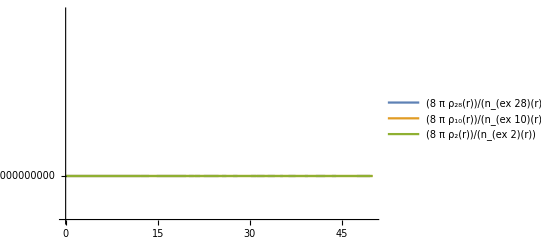

```mathematica
Plot[{8Pi Subscript[ρ, 28][r]/Subscript[n, ex(28)][r],8Pi Subscript[ρ, 10][r]/Subscript[n, ex(10)][r],8Pi Subscript[ρ, 2][r]/Subscript[n, ex(2)][r]},{r,0,50},PlotLegends->"Expressions"]
```

```mathematica
MeijerGReduce[{(x+c)^-4},x]
```

```mathematica
{ConditionalExpression[MeijerG[{{-3},{}},{{0},{}},x/c]/(6 c^4),Re[c]>0]}
```

```mathematica
MeijerGReduce[{BesselJ[3,x]},x]
```

```mathematica
{MeijerG[{{},{}},{{3},{0}},x/2,1/2]}
```

{MeijerG[{{},{}},{{3},{0}},x/2,1/2]}

```mathematica
{x^(3/2) MeijerG[{{},{}},{{3},{0}},x/2,1/2]}
```

```mathematica
Integrate[MeijerG[{{-3},{}},{{0},{}},x/c]MeijerG[{{},{}},{{3},{0}},x/2,1/2],{x,0,Infinity}]
```

```mathematica
∫_0^∞ MeijerG[{{-3},{}},{{0},{}},x/c] MeijerG[{{},{}},{{3},{0}},x]ⅆx
```

```mathematica
∫_0^∞ MeijerG[{{},{}},{{3},{0}},x] MeijerG[{{-3},{}},{{0},{}},x/c]ⅆ
```

```mathematica
Solve[r^2(u+2/x)==z,x]
```

{{x→-(2 r^2)/(r^2 u-z)}}

```mathematica
D[-(2 r^2)/(r^2 u-z),z]
```

-(2 r^2)/((r^2 u-z)^2)

```mathematica
D[(x+1)^-3,x]
```

-3/(1+x)^4

```mathematica
MeijerG[{{},{-3}},{{0,-3},{0}},0.164414 r^2]
```

BesselJ[0,0.81096 r]

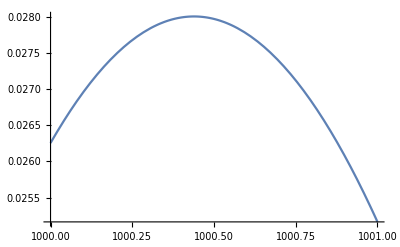

```mathematica
Plot[BesselJ[0,0.8109599250271249 r],{r,1000,1001}]
```

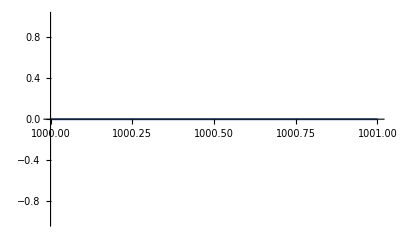

```mathematica
Plot[-2 BesselK[0,0.8109599250271249 √(r^2)],{r,1000,1001}]
```

```mathematica
MeijerG[{{},{1}},{{0,1},{0}},0.164414 r^2]
```

BesselJ[0,0.81096 r]

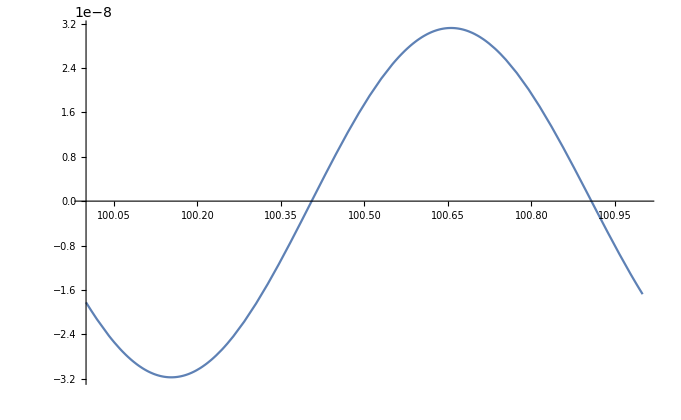

```mathematica
Plot[r^-3 BesselJ[0, r/0.16],{r,100,101}]
```

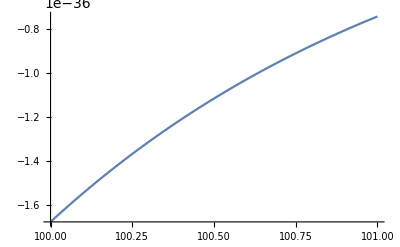

```mathematica
Plot[-2 BesselK[0,0.8109599250271249 √(r^2)],{r,100,101}]
```

```mathematica
Subscript[G, 0,2]^(2,0)(0.164414 r^2|{{0,0}})
```

2 BesselK[0,0.81096 √(r^2)]

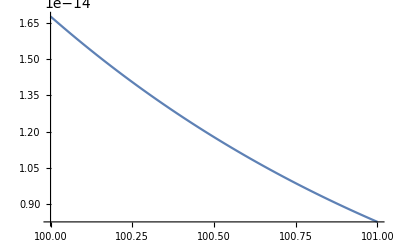

```mathematica
Plot[2 r^11 BesselK[0,0.8109599250271249 r],{r,100,101}]
```

```mathematica
MeijerG[{{},{}},{{0},{0}},0.164414 r^2]
```

BesselJ[0,0.81096 r]

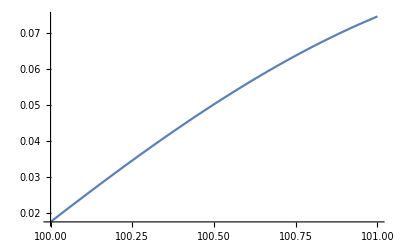

```mathematica
Plot[BesselJ[0,0.8109599250271249 r],{r,100,101}]
```

```mathematica
MeijerGReduce[{x^2 Sqrt[-0.164414+2/x]^3 BesselJ[3,2r Sqrt[-0.164414+2/x]]},x]
```

{(-0.164414+2/x)^(3/2) x^2 BesselJ[3,2 r √(-0.164414+2/x)]}

```mathematica
MeijerGReduce[BesselJ[3,x],x]
```

```mathematica
MeijerG[{{},{}},{{3/2},{-3/2}},x/2,1/2]-MeijerG[{{},{}},{{3/2},{-3/2}},x^2/4]
```

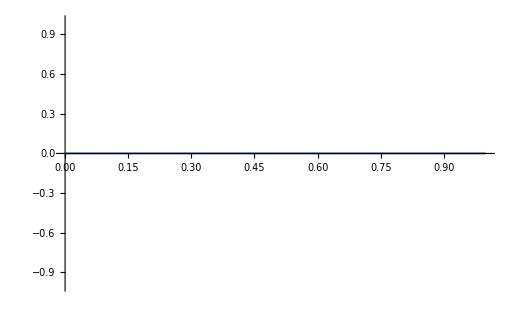

```mathematica
Plot[-MeijerG[{{},{}},{{3/2},{-3/2}},x^2/4]+MeijerG[{{},{}},{{3/2},{-3/2}},x/2,1/2],{x,0,1}]
```

```mathematica
Plot[r^-3 Sum[x^2 Sqrt[-0.164414+2/Max[x,0.00005]]^3 BesselJ[3,2r Sqrt[-0.164414+2/x]](0.0001),{x,0,2/0.164414,0.0001}],{r,100,101}]
```

$Aborted

```mathematica
Subscript[G, 1,1]^(1,1)(x|{{-3}, {0}})
```

6/(1+x)^4

```mathematica
Subscript[G, 0,2]^(1,0)(x|{{-1,-4}})
```

```mathematica
Integrate[Subscript[G, 0,2]^(1,0)(x|{{-1,-4}})Subscript[G, 1,1]^(1,1)(x/c|{{1}, {4}}),{x,0,Infinity}]
```

```mathematica
2 BesselK[0,2 Sqrt[0.164414]r]
```

2 BesselK[0,0.81096 r]

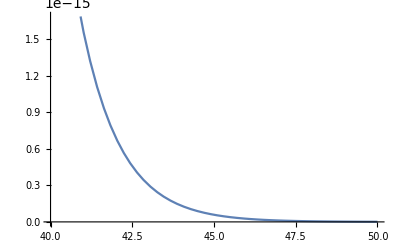

```mathematica
Plot[2 BesselK[0,0.8109599250271249 r],{r,40,50}]
```

```mathematica
MeijerG[{{},{}},{{},{}},x]
```

```mathematica
Integrate[Subscript[G, 0,2]^(1,0)(x|{{-1,-4}})Subscript[G, 1,1]^(1,1)(x/c|{{1}, {4}}),{x,0,Infinity}]
```

```mathematica
Integrate[Subscript[G, 0,2]^(1,0)(x|{{3,0}})Subscript[G, 1,1]^(1,1)(x/c|{{-3}, {0}}),{x,0,Infinity}]
```

ConditionalExpression[2 c^4 BesselK[0,2 √c],Im[c]≠0||Re[c]≥0]

```mathematica
2 BesselK[0,2 √(0.164414 r^2)]
```

2 BesselK[0,0.81096 √(r^2)]

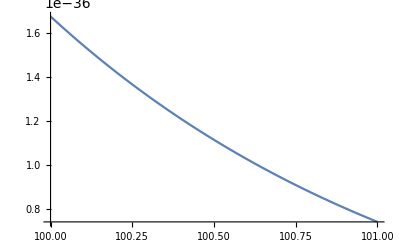

```mathematica
Plot[2 BesselK[0,0.8109599250271249 √(r^2)],{r,100,101}]
```

```mathematica
Integrate[Subscript[G, 0,2]^(1,0)(x|{{-1,-4}})Subscript[G, 1,1]^(1,1)(x/c|{{1}, {4}}),{x,0,Infinity}]
```

ConditionalExpression[2 BesselK[0,2 √c],Im[c]≠0||Re[c]≥0]

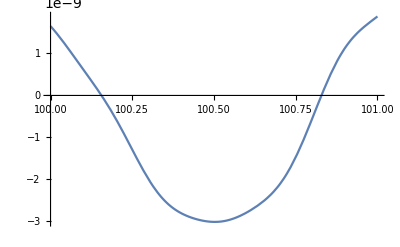

```mathematica
Plot[r^-3 Sum[x^2 Sqrt[-0.164414+2/Max[x,0.005]]^3 BesselJ[3,2r Sqrt[-0.164414+2/x]](0.01),{x,0,2/0.164414,0.01}],{r,100,101}]
```

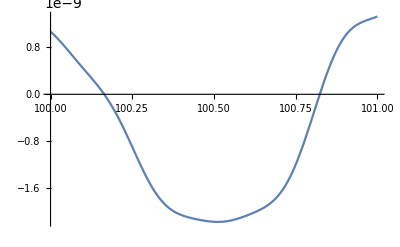

```mathematica
Plot[Sum[1/(2 π r)(x (2/Max[x,0.005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.01),{x,0,2/0.164414,0.01}],{r,100,101}]
```

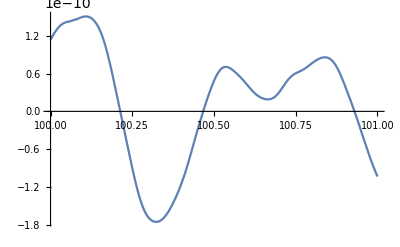

```mathematica
Plot[r^-3 Sum[x^2 Sqrt[-0.164414+2/Max[x,0.0005]]^3 BesselJ[3,2r Sqrt[-0.164414+2/x]](0.001),{x,0,2/0.164414,0.001}],{r,100,101}]
```

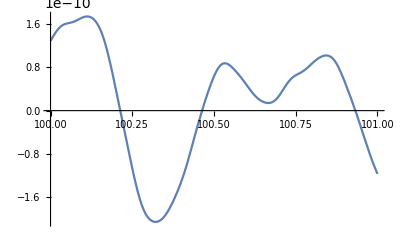

```mathematica
Plot[Sum[1/(2 π r)(x (2/Max[x,0.0005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.164414,0.001}],{r,100,101}]
```

```mathematica
Plot[Sum[1/(2 π r)(x (2/Max[x,0.00005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.164414,0.001}],{r,100,101}]
```

Power::infy: Infinite expression 1/0. encountered.

$Aborted

```mathematica
Plot[Sum[1/(2 π r)(x (2/Max[x,0.00005]-0.164414)^2) (Hypergeometric0F1[3,-(2/Max[x,0.00005]-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/Max[x,0.00005]-0.164414) (x^2+r^2+2 x r)])(0.001),{x,0,2/0.164414,0.001}],{r,100,101}]
```

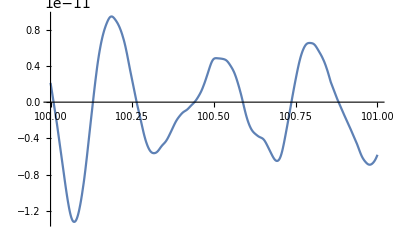

```mathematica
Plot[r^-3 Sum[x^2 Sqrt[-0.164414+2/Max[x,0.00005]]^3 BesselJ[3,2r Sqrt[-0.164414+2/x]](0.0001),{x,0,2/0.164414,0.0001}],{r,100,101}]
```

```mathematica
Plot[Sum[1/(2 π r)(x (2/Max[x,0.00005]-0.164414)^2) (Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]-Hypergeometric0F1[3,-(2/x-0.164414) (x^2+r^2+2 x r)])(0.0001),{x,0,2/0.164414,0.0001}],{r,100,101}]
```

$Aborted

```mathematica
Plot[r^-3 Sum[x^2 Sqrt[-0.164414+2/Max[x,0.000005]]^3 BesselJ[3,2r Sqrt[-0.164414+2/x]](0.00001),{x,0,2/0.164414,0.00001}],{r,100,101}]
```

$Aborted

```mathematica
D[r^-3 BesselJ[3,2r Sqrt[u+2/x]],r]
```

-(3 BesselJ[3,2 r √(u+2/x)])/r^4+(√(u+2/x) (BesselJ[2,2 r √(u+2/x)]-BesselJ[4,2 r √(u+2/x)]))/r^3

```mathematica
D[-(3 BesselJ[3,2 r √(u+2/x)])/r^4+(√(u+2/x) (BesselJ[2,2 r √(u+2/x)]-BesselJ[4,2 r √(u+2/x)]))/r^3,r]
```

(12 BesselJ[3,2 r √(u+2/x)])/r^5-(6 √(u+2/x) (BesselJ[2,2 r √(u+2/x)]-BesselJ[4,2 r √(u+2/x)]))/r^4+(√(u+2/x) (√(u+2/x) (BesselJ[1,2 r √(u+2/x)]-BesselJ[3,2 r √(u+2/x)])-√(u+2/x) (BesselJ[3,2 r √(u+2/x)]-BesselJ[5,2 r √(u+2/x)])))/r^3

```mathematica
r^2((12 BesselJ[3,2 r √(-0.164414+2/x)])/r^5-(6 √(-0.164414+2/x) (BesselJ[2,2 r √(-0.164414+2/x)]-BesselJ[4,2 r √(-0.164414+2/x)]))/r^4+1/r^3 √(-0.164414+2/x) (√(-0.164414+2/x) (BesselJ[1,2 r √(-0.164414+2/x)]-BesselJ[3,2 r √(-0.164414+2/x)])-√(-0.164414+2/x) (BesselJ[3,2 r √(-0.164414+2/x)]-BesselJ[5,2 r √(-0.164414+2/x)])))+(-(3 BesselJ[3,2 r √(-0.164414+2/x)])/r^4+(√(-0.164414+2/x) (BesselJ[2,2 r √(-0.164414+2/x)]-BesselJ[4,2 r √(-0.164414+2/x)]))/r^3)r-(2Sqrt[0.164414]r)^2 r^-3 BesselJ[3,2r Sqrt[u+2/x]]
```

-(0.657656 BesselJ[3,2 r √(u+2/x)])/r+r (-(3 BesselJ[3,2 r √(-0.164414+2/x)])/r^4+(√(-0.164414+2/x) (BesselJ[2,2 r √(-0.164414+2/x)]-BesselJ[4,2 r √(-0.164414+2/x)]))/r^3)+r^2 ((12 BesselJ[3,2 r √(-0.164414+2/x)])/r^5-(6 √(-0.164414+2/x) (BesselJ[2,2 r √(-0.164414+2/x)]-BesselJ[4,2 r √(-0.164414+2/x)]))/r^4+1/r^3 √(-0.164414+2/x) (√(-0.164414+2/x) (BesselJ[1,2 r √(-0.164414+2/x)]-BesselJ[3,2 r √(-0.164414+2/x)])-√(-0.164414+2/x) (BesselJ[3,2 r √(-0.164414+2/x)]-BesselJ[5,2 r √(-0.164414+2/x)])))

```mathematica
Simplify[%9]
```

```mathematica
1/(r^3 x)(r^2 (2.-0.164414 x) BesselJ[1,2 r √(-0.164414+2/x)]-5. r √(-0.164414+2/x) x BesselJ[2,2 r √(-0.164414+2/x)]-4. r^2 BesselJ[3,2 r √(-0.164414+2/x)]+9. x BesselJ[3,2 r √(-0.164414+2/x)]+0.328828 r^2 x BesselJ[3,2 r √(-0.164414+2/x)]-0.657656 r^2 x BesselJ[3,2 r √(-0.164414+2/x)]+5. r √(-0.164414+2/x) x BesselJ[4,2 r √(-0.164414+2/x)]+2. r^2 BesselJ[5,2 r √(-0.164414+2/x)]-0.164414 r^2 x BesselJ[5,2 r √(-0.164414+2/x)])
```

1/(r^3 x)(r^2 (2.-0.164414 x) BesselJ[1,2 r √(-0.164414+2/x)]-5. r √(-0.164414+2/x) x BesselJ[2,2 r √(-0.164414+2/x)]-4. r^2 BesselJ[3,2 r √(-0.164414+2/x)]+9. x BesselJ[3,2 r √(-0.164414+2/x)]-0.328828 r^2 x BesselJ[3,2 r √(-0.164414+2/x)]+5. r √(-0.164414+2/x) x BesselJ[4,2 r √(-0.164414+2/x)]+2. r^2 BesselJ[5,2 r √(-0.164414+2/x)]-0.164414 r^2 x BesselJ[5,2 r √(-0.164414+2/x)])

```mathematica
Manipulate[Plot[%12,{x,0,2/0.164414}],{r,100,1000}]
```

```mathematica
Hypergeometric0F1[3,-(2/x-0.164414) (x^2-2 r x+r^2)]
```

```mathematica
Hypergeometric0F1[3,(0.164414-2/x) (r^2-2 r x+x^2)]-BesselJ[2,2Sqrt[(2/x-0.164414) (x^2-2 r x+r^2)]](Sqrt[(2/x-0.164414) (x^2-2 r x+r^2)])^-3 Gamma[4]
```

-(6 BesselJ[2,2 √((-0.164414+2/x) (r^2-2 r x+x^2))])/(((-0.164414+2/x) (r^2-2 r x+x^2))^(3/2))+Hypergeometric0F1[3,(0.164414-2/x) (r^2-2 r x+x^2)]

```mathematica
BesselJ[2,2Sqrt[(2/x-0.164414) (x^2-2 r x+r^2)]](Sqrt[(2/x-0.164414) (x^2-2 r x+r^2)])^-3
```

```mathematica
Solve[z==(2/x+u) (x^2-2 r x+r^2),x]
```

{{x→(2 (-1+r u))/(3 u)+(2^(1/3) (-4-4 r u-r^2 u^2-3 u z))/(3 u (16+24 r u+12 r^2 u^2+2 r^3 u^3+18 u z-18 r u^2 z+√(4 (-4-4 r u-r^2 u^2-3 u z)^3+(16+24 r u+12 r^2 u^2+2 r^3 u^3+18 u z-18 r u^2 z)^2))^(1/3))-((16+24 r u+12 r^2 u^2+2 r^3 u^3+18 u z-18 r u^2 z+√(4 (-4-4 r u-r^2 u^2-3 u z)^3+(16+24 r u+12 r^2 u^2+2 r^3 u^3+18 u z-18 r u^2 z)^2))^(1/3))/(3 2^(1/3) u)},{x→(2 (-1+r u))/(3 u)-((1+ⅈ √3) (-4-4 r u-r^2 u^2-3 u z))/(3 2^(2/3) u (16+24 r u+12 r^2 u^2+2 r^3 u^3+18 u z-18 r u^2 z+√(4 (-4-4 r u-r^2 u^2-3 u z)^3+(16+24 r u+12 r^2 u^2+2 r^3 u^3+18 u z-18 r u^2 z)^2))^(1/3))+((1-ⅈ √3) (16+24 r u+12 r^2 u^2+2 r^3 u^3+18 u z-18 r u^2 z+√(4 (-4-4 r u-r^2 u^2-3 u z)^3+(16+24 r u+12 r^2 u^2+2 r^3 u^3+18 u z-18 r u^2 z)^2))^(1/3))/(6 2^(1/3) u)},{x→(2 (-1+r u))/(3 u)-((1-ⅈ √3) (-4-4 r u-r^2 u^2-3 u z))/(3 2^(2/3) u (16+24 r u+12 r^2 u^2+2 r^3 u^3+18 u z-18 r u^2 z+√(4 (-4-4 r u-r^2 u^2-3 u z)^3+(16+24 r u+12 r^2 u^2+2 r^3 u^3+18 u z-18 r u^2 z)^2))^(1/3))+((1+ⅈ √3) (16+24 r u+12 r^2 u^2+2 r^3 u^3+18 u z-18 r u^2 z+√(4 (-4-4 r u-r^2 u^2-3 u z)^3+(16+24 r u+12 r^2 u^2+2 r^3 u^3+18 u z-18 r u^2 z)^2))^(1/3))/(6 2^(1/3) u)}}

```mathematica
Solve[z==2k Sqrt[x^2+r^2-2x r t],t]
```

{{t→(4 k^2 r^2+4 k^2 x^2-z^2)/(8 k^2 r x)}}

```mathematica
Solve[z==b Sqrt[1-c t],t]
```

{{t→(b^2-z^2)/(b^2 c)}}

```mathematica
Solve[(1-c t)b^2/4==z,t]
```

{{t→(b^2-4 z)/(b^2 c)}}

```mathematica
D[(b^2-4 z)/(b^2 c),z]
```

-4/(b^2 c)

```mathematica
MeijerGReduce[BesselJ[3,b Sqrt[1-c t]],b]
```

MeijerG[{{},{}},{{3/2},{-3/2}},1/2 b √(1-c t),1/2]

```mathematica
Solve[(1-c t)d^2==z,t]
```

{{t→(d^2-z)/(c d^2)}}

```mathematica
D[(d^2-z)/(c d^2),z]
```

-1/(c d^2)

```mathematica
MeijerGReduce[]
```

```mathematica
Reduce[Sqrt[x^2+r^2-2x r t]^3,k^2(x^2+r^2-2x r t)]
```

Reduce::ivar: k^2 (r^2-2 r t x+x^2) is not a valid variable.

Reduce[(r^2-2 r t x+x^2)^(3/2),k^2 (r^2-2 r t x+x^2)]

```mathematica
Integrate[z^(-3/2)MeijerG[{{},{}},{{3/2},{-3/2}},z],z]
```

Integrate::ilim: Invalid integration variable or limit(s) in k^2 (r^2-2 r t x+x^2).

∫BesselJ[3,2 k √(r^2-2 r t x+x^2)]/(k^3 (r^2-2 r t x+x^2)^(3/2))ⅆ(k^2 (r^2-2 r t x+x^2))

```mathematica
Integrate[y^(-3/2)MeijerG[{{},{}},{{3/2},{-3/2}},y],y]
```

```mathematica
((1-c t)d^2-2 BesselJ[2,2 √((1-c t)d^2)])/((1-c t)d^2)
```

```mathematica
-2 BesselJ[2,2 √((1-c )d^2)]/(1-c )d^2-(-2 BesselJ[2,2 √((1+c )d^2)]/(1+c )d^2)
```

```mathematica
(-(2 d^2 BesselJ[2,2 √((1-c) d^2)])/(1-c)+(2 d^2 BesselJ[2,2 √((1+c) d^2)])/(1+c))(-4/(b^2 c))*k^6
```

-(4 k^6 (-(2 d^2 BesselJ[2,2 √((1-c) d^2)])/(1-c)+(2 d^2 BesselJ[2,2 √((1+c) d^2)])/(1+c)))/(b^2 c)

```mathematica
d=k Sqrt[x^2+r^2]
c=(2x r/(x^2+r^2))
```

```mathematica
-(4 (-(2 (k Sqrt[x^2+r^2])^2 BesselJ[2,2 √((1-(2x r/(x^2+r^2))) (k Sqrt[x^2+r^2])^2)])/(1-(2x r/(x^2+r^2)))+(2 d^2 BesselJ[2,2 √((1+(2x r/(x^2+r^2))) (k Sqrt[x^2+r^2])^2)])/(1+(2x r/(x^2+r^2)))))/((k Sqrt[x^2+r^2])^2 (2x r/(x^2+r^2)))k^6 x^2
```

-(2 k^4 x (-(2 k^2 (r^2+x^2) BesselJ[2,2 √(k^2 (r^2+x^2) (1-(2 r x)/(r^2+x^2)))])/(1-(2 r x)/(r^2+x^2))+(2 d^2 BesselJ[2,2 √(k^2 (r^2+x^2) (1+(2 r x)/(r^2+x^2)))])/(1+(2 r x)/(r^2+x^2))))/r

```mathematica
Mei
```

```mathematica
2 √((u+2/x) (r^2+x^2) (1-(2 r x)/(r^2+x^2)))
```

```mathematica
Simplify[(u+2/x) (r^2+x^2) (1-(2 r x)/(r^2+x^2))]
```

((r-x)^2 (2+u x))/x

```mathematica
Solve[((r-x)^2 2)/x==z,x]
```

{{x→(2 (1+k^2 r t))/(3 k^2)+(2^(1/3) (-3 k^2 (-4 r-k^2 r^2)-4 (1+k^2 r t)^2))/(3 k^2 (-16+72 k^2 r-36 k^4 r^2-48 k^2 r t+72 k^4 r^2 t+18 k^6 r^3 t-48 k^4 r^2 t^2-16 k^6 r^3 t^3+√((-16+72 k^2 r-36 k^4 r^2-48 k^2 r t+72 k^4 r^2 t+18 k^6 r^3 t-48 k^4 r^2 t^2-16 k^6 r^3 t^3)^2+4 (-3 k^2 (-4 r-k^2 r^2)-4 (1+k^2 r t)^2)^3))^(1/3))-1/(3 2^(1/3) k^2)(-16+72 k^2 r-36 k^4 r^2-48 k^2 r t+72 k^4 r^2 t+18 k^6 r^3 t-48 k^4 r^2 t^2-16 k^6 r^3 t^3+√((-16+72 k^2 r-36 k^4 r^2-48 k^2 r t+72 k^4 r^2 t+18 k^6 r^3 t-48 k^4 r^2 t^2-16 k^6 r^3 t^3)^2+4 (-3 k^2 (-4 r-k^2 r^2)-4 (1+k^2 r t)^2)^3))^(1/3)},{x→(2 (1+k^2 r t))/(3 k^2)-((1+ⅈ √3) (-3 k^2 (-4 r-k^2 r^2)-4 (1+k^2 r t)^2))/(3 2^(2/3) k^2 (-16+72 k^2 r-36 k^4 r^2-48 k^2 r t+72 k^4 r^2 t+18 k^6 r^3 t-48 k^4 r^2 t^2-16 k^6 r^3 t^3+√((-16+72 k^2 r-36 k^4 r^2-48 k^2 r t+72 k^4 r^2 t+18 k^6 r^3 t-48 k^4 r^2 t^2-16 k^6 r^3 t^3)^2+4 (-3 k^2 (-4 r-k^2 r^2)-4 (1+k^2 r t)^2)^3))^(1/3))+1/(6 2^(1/3) k^2)(1-ⅈ √3) (-16+72 k^2 r-36 k^4 r^2-48 k^2 r t+72 k^4 r^2 t+18 k^6 r^3 t-48 k^4 r^2 t^2-16 k^6 r^3 t^3+√((-16+72 k^2 r-36 k^4 r^2-48 k^2 r t+72 k^4 r^2 t+18 k^6 r^3 t-48 k^4 r^2 t^2-16 k^6 r^3 t^3)^2+4 (-3 k^2 (-4 r-k^2 r^2)-4 (1+k^2 r t)^2)^3))^(1/3)},{x→(2 (1+k^2 r t))/(3 k^2)-((1-ⅈ √3) (-3 k^2 (-4 r-k^2 r^2)-4 (1+k^2 r t)^2))/(3 2^(2/3) k^2 (-16+72 k^2 r-36 k^4 r^2-48 k^2 r t+72 k^4 r^2 t+18 k^6 r^3 t-48 k^4 r^2 t^2-16 k^6 r^3 t^3+√((-16+72 k^2 r-36 k^4 r^2-48 k^2 r t+72 k^4 r^2 t+18 k^6 r^3 t-48 k^4 r^2 t^2-16 k^6 r^3 t^3)^2+4 (-3 k^2 (-4 r-k^2 r^2)-4 (1+k^2 r t)^2)^3))^(1/3))+1/(6 2^(1/3) k^2)(1+ⅈ √3) (-16+72 k^2 r-36 k^4 r^2-48 k^2 r t+72 k^4 r^2 t+18 k^6 r^3 t-48 k^4 r^2 t^2-16 k^6 r^3 t^3+√((-16+72 k^2 r-36 k^4 r^2-48 k^2 r t+72 k^4 r^2 t+18 k^6 r^3 t-48 k^4 r^2 t^2-16 k^6 r^3 t^3)^2+4 (-3 k^2 (-4 r-k^2 r^2)-4 (1+k^2 r t)^2)^3))^(1/3)}}

```mathematica
f=y-((r-x)^2 2)/x
```

```mathematica
D[((r-x)^2 2)/x,x]
```

```mathematica
Simplify[-(2 (r-x)^2)/x^2-(4 (r-x))/x]
```

2-(2 r^2)/x^2

```mathematica
Solve[(x-r)Sqrt[u+2/x]==p,x]
```

{{x→(2 (-1+r u))/(3 u)-(2^(1/3) (-4-3 p^2 u-4 r u-r^2 u^2))/(3 u (-16-18 p^2 u-24 r u+18 p^2 r u^2-12 r^2 u^2-2 r^3 u^3+√(4 (-4-3 p^2 u-4 r u-r^2 u^2)^3+(-16-18 p^2 u-24 r u+18 p^2 r u^2-12 r^2 u^2-2 r^3 u^3)^2))^(1/3))+((-16-18 p^2 u-24 r u+18 p^2 r u^2-12 r^2 u^2-2 r^3 u^3+√(4 (-4-3 p^2 u-4 r u-r^2 u^2)^3+(-16-18 p^2 u-24 r u+18 p^2 r u^2-12 r^2 u^2-2 r^3 u^3)^2))^(1/3))/(3 2^(1/3) u)},{x→(2 (-1+r u))/(3 u)+((1+ⅈ √3) (-4-3 p^2 u-4 r u-r^2 u^2))/(3 2^(2/3) u (-16-18 p^2 u-24 r u+18 p^2 r u^2-12 r^2 u^2-2 r^3 u^3+√(4 (-4-3 p^2 u-4 r u-r^2 u^2)^3+(-16-18 p^2 u-24 r u+18 p^2 r u^2-12 r^2 u^2-2 r^3 u^3)^2))^(1/3))-((1-ⅈ √3) (-16-18 p^2 u-24 r u+18 p^2 r u^2-12 r^2 u^2-2 r^3 u^3+√(4 (-4-3 p^2 u-4 r u-r^2 u^2)^3+(-16-18 p^2 u-24 r u+18 p^2 r u^2-12 r^2 u^2-2 r^3 u^3)^2))^(1/3))/(6 2^(1/3) u)},{x→(2 (-1+r u))/(3 u)+((1-ⅈ √3) (-4-3 p^2 u-4 r u-r^2 u^2))/(3 2^(2/3) u (-16-18 p^2 u-24 r u+18 p^2 r u^2-12 r^2 u^2-2 r^3 u^3+√(4 (-4-3 p^2 u-4 r u-r^2 u^2)^3+(-16-18 p^2 u-24 r u+18 p^2 r u^2-12 r^2 u^2-2 r^3 u^3)^2))^(1/3))-((1+ⅈ √3) (-16-18 p^2 u-24 r u+18 p^2 r u^2-12 r^2 u^2-2 r^3 u^3+√(4 (-4-3 p^2 u-4 r u-r^2 u^2)^3+(-16-18 p^2 u-24 r u+18 p^2 r u^2-12 r^2 u^2-2 r^3 u^3)^2))^(1/3))/(6 2^(1/3) u)}}

```mathematica
Solve[(x-r)Sqrt[2/x]==p,x]
```

{{x→1/4 (p^2+4 r-√(p^4+8 p^2 r))},{x→1/4 (p^2+4 r+√(p^4+8 p^2 r))}}

```mathematica
D[(x-r)Sqrt[2/x],x]
```

√2 √(1/x)-((1/x)^(3/2) (-r+x))/(√2)

```mathematica
1/(√2 √(1/(1/4 (p^2+4 r-√(p^4+8 p^2 r))))-((1/(1/4 (p^2+4 r-√(p^4+8 p^2 r))))^(3/2) (-r+1/4 (p^2+4 r-√(p^4+8 p^2 r))))/(√2))/(1/4 (p^2+4 r-√(p^4+8 p^2 r)))
```

```mathematica
Simplify[4/((p^2+4 r-√(p^4+8 p^2 r)) (2 √2 √(1/(p^2+4 r-√(p^4+8 p^2 r)))-4 √2 (1/(p^2+4 r-√(p^4+8 p^2 r)))^(3/2) (-r+1/4 (p^2+4 r-√(p^4+8 p^2 r)))))]
```

-2/(√(1/(2 p^2+8 r-2 √(p^4+8 p^2 r))) (-p^2-8 r+√(p^4+8 p^2 r)))

```mathematica
Solve[(x-r)^2((2+u)/x)==p,x]
```

{{x→(p+4 r+2 r u-√p √(p+8 r+4 r u))/(2 (2+u))},{x→(p+4 r+2 r u+√p √(p+8 r+4 r u))/(2 (2+u))}}

```mathematica
Solve[(x-r)^2(2/x)==p,x]                     (*1*)
```

{{x→1/4 (p+4 r-√p √(p+8 r))},{x→1/4 (p+4 r+√p √(p+8 r))}}

```mathematica
D[(x-r)^2(2/x),x]
```

(4 (-r+x))/x-(2 (-r+x)^2)/x^2

```mathematica
Simplify[(4 (-r+x))/x-(2 (-r+x)^2)/x^2]        (*2*)
```

2-(2 r^2)/x^2

```mathematica
(1/4 (p+4 r-√p √(p+8 r)))/(-r+(1/4 (p+4 r-√p √(p+8 r))))^4(2-(2 r^2)/(1/4 (p+4 r-√p √(p+8 r)))^2)^-1+(2-(2 r^2)/(1/4 (p+4 r+√p √(p+8 r)))^2)^-1(1/4 (p+4 r+√p √(p+8 r)))/(-r+(1/4 (p+4 r+√p √(p+8 r))))^4
```

(p+4 r-√p √(p+8 r))/(4 (2-(32 r^2)/(p+4 r-√p √(p+8 r))^2) (-r+1/4 (p+4 r-√p √(p+8 r)))^4)+(p+4 r+√p √(p+8 r))/(4 (2-(32 r^2)/(p+4 r+√p √(p+8 r))^2) (-r+1/4 (p+4 r+√p √(p+8 r)))^4)

```mathematica
Simplify[%22]
```

0

```mathematica
(1/4 (p+4 r-√p √(p+8 r))-r)^-2(2-(2 r^2)/(1/4 (p+4 r-√p √(p+8 r)))^2)^-1+(2-(2 r^2)/(1/4 (p+4 r+√p √(p+8 r)))^2)^-1(1/4 (p+4 r+√p √(p+8 r))-r)^-2
```

1/((2-(32 r^2)/(p+4 r-√p √(p+8 r))^2) (-r+1/4 (p+4 r-√p √(p+8 r)))^2)+1/((2-(32 r^2)/(p+4 r+√p √(p+8 r))^2) (-r+1/4 (p+4 r+√p √(p+8 r)))^2)

```mathematica
Simplify[1/((2-(32 r^2)/(p+4 r-√p √(p+8 r))^2) (-r+1/4 (p+4 r-√p √(p+8 r)))^2)+1/((2-(32 r^2)/(p+4 r+√p √(p+8 r))^2) (-r+1/4 (p+4 r+√p √(p+8 r)))^2)]
```

0

```mathematica
Simplify[4/((p+4 r-√p √(p+8 r)) (2-(32 r^2)/(p+4 r-√p √(p+8 r))^2))+4/((p+4 r+√p √(p+8 r)) (2-(32 r^2)/(p+4 r+√p √(p+8 r))^2))]
```

0

```mathematica
Simplify[(4 (2-(32 r^2)/(p+4 r-√p √(p+8 r))^2))/(p+4 r-√p √(p+8 r))+(4 (2-(32 r^2)/(p+4 r+√p √(p+8 r))^2))/(p+4 r+√p √(p+8 r))]
```

```mathematica
-(p (p^2+12 p r+32 r^2))/(4 r^4)                                    (*3*)
```

```mathematica
MeijerGReduce[-(p (p^2+12 p r+32 r^2))/(4 r^4),p]
```

-(p (p^2+12 p r+32 r^2))/(4 r^4)

```mathematica
FullSimplify[-(p (p^2+12 p r+32 r^2))/(4 r^4)]
```

-(p (p+4 r) (p+8 r))/(4 r^4)

```mathematica
Expand[-(p (p+4 r) (p+8 r))/(4 r^4)]
```

-p^3/(4 r^4)-(3 p^2)/r^3-(8 p)/r^2

```mathematica
Simplify[((p+4 r+2 r u-√p √(p+8 r+4 r u))/(2 (2+u)))^-1(2-(2 r^2)/((p+4 r+2 r u-√p √(p+8 r+4 r u))/(2 (2+u)))^2)+(2-(2 r^2)/((p+4 r+2 r u+√p √(p+8 r+4 r u))/(2 (2+u)))^2)((p+4 r+2 r u+√p √(p+8 r+4 r u))/(2 (2+u)))^-1]
```

-(2 p (p^2+6 p r (2+u)+8 r^2 (2+u)^2))/(r^4 (2+u)^3)

```mathematica
Expand[-(2 p (p^2+6 p r (2+u)+8 r^2 (2+u)^2))/(r^4 (2+u)^3)]
```

```mathematica
-(2 p^3)/(r^4 (2+u)^3)-(24 p^2)/(r^3 (2+u)^3)-(64 p)/(r^2 (2+u)^3)-(12 p^2 u)/(r^3 (2+u)^3)-(64 p u)/(r^2 (2+u)^3)-(16 p u^2)/(r^2 (2+u)^3)(*3.5*)
```

```mathematica
Solve[(x+r)^2(2/x)==p,x](*1*)
```

{{x→1/4 (p-4 r-√(p^2-8 p r))},{x→1/4 (p-4 r+√(p^2-8 p r))}}

```mathematica
D[(x+r)^2(2/x),x]
```

(4 (r+x))/x-(2 (r+x)^2)/x^2

```mathematica
Simplify[(4 (r+x))/x-(2 (r+x)^2)/x^2]
```

2-(2 r^2)/x^2

```mathematica
(2-(2 r^2)/((1/4 (p-4 r-√(p^2-8 p r)))^2))^-1(1/4 (p-4 r-√(p^2-8 p r)))^-1+(2-(2 r^2)/((1/4 (p-4 r+√(p^2-8 p r)))^2))^-1(1/4 (p-4 r+√(p^2-8 p r)))^-1
```

4/((p-4 r-√(p^2-8 p r)) (2-(32 r^2)/((p-4 r-√(p^2-8 p r))^2)))+4/((p-4 r+√(p^2-8 p r)) (2-(32 r^2)/((p-4 r+√(p^2-8 p r))^2)))

```mathematica
Simplify[4/((p-4 r-√(p^2-8 p r)) (2-(32 r^2)/((p-4 r-√(p^2-8 p r))^2)))+4/((p-4 r+√(p^2-8 p r)) (2-(32 r^2)/((p-4 r+√(p^2-8 p r))^2)))]
```

0

```mathematica
Simplify[8/((p-4 r-√(p^2-8 p r)) (2-(32 r^2)/((p-4 r-√(p^2-8 p r))^2)))]
```

8/((p-√(p (p-8 r))-4 r) (2-(32 r^2)/(-p+√(p (p-8 r))+4 r)^2))

```mathematica
MeijerGReduce[(2 (-p+√(p (p-8 r))+4 r))/(-p^2-4 √(p (p-8 r)) r+p (√(p (p-8 r))+8 r)),p]
```

(2 (-p+√(p (p-8 r))+4 r))/(-p^2-4 √(p (p-8 r)) r+p (√(p (p-8 r))+8 r))

```mathematica
Cancel[8/((p-√(p (p-8 r))-4 r) (2-(32 r^2)/(-p+√(p (p-8 r))+4 r)^2))]
```

(2 (-p+√(p (p-8 r))+4 r))/(-p^2+p √(p (p-8 r))+8 p r-4 √(p (p-8 r)) r)

```mathematica
Simplify[(2 (-p+√(p (p-8 r))+4 r))/(-p^2+p √(p (p-8 r))+8 p r-4 √(p (p-8 r)) r)]
```

(2 (-p+√(p (p-8 r))+4 r))/(-p^2-4 √(p (p-8 r)) r+p (√(p (p-8 r))+8 r))

```mathematica
x/(x-r)^4
```

x/(-r+x)^4

```mathematica
(p+4 r+2 r u-√p √(p+8 r+4 r u))/(2 (2+u))
```

```mathematica
(((p+4 r+2 r u-√p √(p+8 r+4 r u))/(2 (2+u)))/(-r+(p+4 r+2 r u-√p √(p+8 r+4 r u))/(2 (2+u)))^4)(2-(2 r^2)/((p+4 r+2 r u-√p √(p+8 r+4 r u))/(2 (2+u)))^2)^-1+(2-(2 r^2)/((p+4 r+2 r u+√p √(p+8 r+4 r u))/(2 (2+u)))^2)^-1((p+4 r+2 r u+√p √(p+8 r+4 r u))/(2 (2+u)))/(-r+((p+4 r+2 r u+√p √(p+8 r+4 r u))/(2 (2+u))))^4
```

(p+4 r+2 r u-√p √(p+8 r+4 r u))/(2 (2+u) (2-(8 r^2 (2+u)^2)/(p+4 r+2 r u-√p √(p+8 r+4 r u))^2) (-r+(p+4 r+2 r u-√p √(p+8 r+4 r u))/(2 (2+u)))^4)+(p+4 r+2 r u+√p √(p+8 r+4 r u))/(2 (2+u) (2-(8 r^2 (2+u)^2)/(p+4 r+2 r u+√p √(p+8 r+4 r u))^2) (-r+(p+4 r+2 r u+√p √(p+8 r+4 r u))/(2 (2+u)))^4)

```mathematica
Simplify[%27]
```

0

```mathematica
Solve[t==(x-r)^2(u+2/x),x]
```

```mathematica
Simplify[1/((2-(32 r^2)/(t+4 r-√t √(t+8 r))^2) (-r+1/4 (t+4 r-√t √(t+8 r)))^2)+1/((2-(32 r^2)/(t+4 r+√t √(t+8 r))^2) (-r+1/4 (t+4 r+√t √(t+8 r)))^2)]
```

0

```mathematica
1/((2-(32 r^2)/(t+4 r-√t √(t+8 r))^2) (-r+1/4 (t+4 r-√t √(t+8 r)))^2)
```

1/((2-(32 r^2)/(4 r+t-√t √(8 r+t))^2) (-r+1/4 (4 r+t-√t √(8 r+t)))^2)

```mathematica
Simplify[1/((2-(32 r^2)/(4 r+t-√t √(8 r+t))^2) (-r+1/4 (4 r+t-√t √(8 r+t)))^2)]
```

16/((t-√t √(8 r+t))^2 (2-(32 r^2)/(4 r+t-√t √(8 r+t))^2))

```mathematica
Cancel[16/((t-√t √(8 r+t))^2 (2-(32 r^2)/(4 r+t-√t √(8 r+t))^2))]
```

(8 (-4 r-t+√t √(8 r+t))^2)/(t^(3/2) (-√t+√(8 r+t))^3 (-8 r-t+√t √(8 r+t)))

```mathematica
1/((2-(32 r^2)/(t+4 r+√t √(t+8 r))^2) (-r+1/4 (t+4 r+√t √(t+8 r)))^2)
```

1/((2-(32 r^2)/(4 r+t+√t √(8 r+t))^2) (-r+1/4 (4 r+t+√t √(8 r+t)))^2)

```mathematica
Simplify[1/((2-(32 r^2)/(4 r+t+√t √(8 r+t))^2) (-r+1/4 (4 r+t+√t √(8 r+t)))^2)]
```

16/((t+√t √(8 r+t))^2 (2-(32 r^2)/(4 r+t+√t √(8 r+t))^2))

```mathematica
Cancel[16/((t+√t √(8 r+t))^2 (2-(32 r^2)/(4 r+t+√t √(8 r+t))^2))]
```

(8 (4 r+t+√t √(8 r+t))^2)/(t^(3/2) (√t+√(8 r+t))^3 (8 r+t+√t √(8 r+t)))

```mathematica
(8 (-4 r-t+√t √(8 r+t))^2)/(t^(3/2) (-√t+√(8 r+t))^3 (-8 r-t+√t √(8 r+t)))+(8 (4 r+t+√t √(8 r+t))^2)/(t^(3/2) (√t+√(8 r+t))^3 (8 r+t+√t √(8 r+t)))
```

(8 (-4 r-t+√t √(8 r+t))^2)/(t^(3/2) (-√t+√(8 r+t))^3 (-8 r-t+√t √(8 r+t)))+(8 (4 r+t+√t √(8 r+t))^2)/(t^(3/2) (√t+√(8 r+t))^3 (8 r+t+√t √(8 r+t)))

```mathematica
Expand[(8 (-4 r-t+√t √(8 r+t))^2)/(t^(3/2) (-√t+√(8 r+t))^3 (-8 r-t+√t √(8 r+t)))+(8 (4 r+t+√t √(8 r+t))^2)/(t^(3/2) (√t+√(8 r+t))^3 (8 r+t+√t √(8 r+t)))]
```

(128 r^2)/(t^(3/2) (-√t+√(8 r+t))^3 (-8 r-t+√t √(8 r+t)))+(128 r)/(√t (-√t+√(8 r+t))^3 (-8 r-t+√t √(8 r+t)))+(16 √t)/((-√t+√(8 r+t))^3 (-8 r-t+√t √(8 r+t)))-(16 √(8 r+t))/((-√t+√(8 r+t))^3 (-8 r-t+√t √(8 r+t)))-(64 r √(8 r+t))/(t (-√t+√(8 r+t))^3 (-8 r-t+√t √(8 r+t)))+(128 r^2)/(t^(3/2) (√t+√(8 r+t))^3 (8 r+t+√t √(8 r+t)))+(128 r)/(√t (√t+√(8 r+t))^3 (8 r+t+√t √(8 r+t)))+(16 √t)/((√t+√(8 r+t))^3 (8 r+t+√t √(8 r+t)))+(16 √(8 r+t))/((√t+√(8 r+t))^3 (8 r+t+√t √(8 r+t)))+(64 r √(8 r+t))/(t (√t+√(8 r+t))^3 (8 r+t+√t √(8 r+t)))

```mathematica
Manipulate[Plot[%49,{r,-8,8}],{t,-8,8}]
```

```mathematica
Simplify[(8 (-4 r-t+√t √(8 r+t))^2)/((-√t+√(8 r+t))^3 (-8 r-t+√t √(8 r+t)))+(8 (4 r+t+√t √(8 r+t))^2)/((√t+√(8 r+t))^3 (8 r+t+√t √(8 r+t)))]
```

0

```mathematica
Hypergeometric0F1[3,-(-0.164414+2/x)(x-r)^2]-Gamma[3]BesselJ[2,2Sqrt[(-0.164414+2/x)](x-r)]/((-0.164414+2/x)(x-r)^2)
```

-(2 BesselJ[2,2 √(-0.164414+2/x) (-r+x)])/((-0.164414+2/x) (-r+x)^2)+Hypergeometric0F1[3,(0.164414-2/x) (-r+x)^2]

```mathematica
Simplify[-(2 BesselJ[2,2 √(-0.164414+2/x) (-r+x)])/((-0.164414+2/x) (-r+x)^2)+Hypergeometric0F1[3,(0.164414-2/x) (-r+x)^2]]
```

(12.1644 x BesselJ[2,2 √(-0.164414+2/x) (-r+x)])/((-1. r+x)^2 (-12.1644+1. x))+Hypergeometric0F1[3,(0.164414-2/x) (r-x)^2]

```mathematica
Manipulate[Plot[(12.16441422263311 x BesselJ[2,2 √(-0.164414+2/x) (-r+x)])/((-1. r+x)^2 (-12.16441422263311+1. x))+Hypergeometric0F1[3,(0.164414-2/x) (r-x)^2],{x,-8,8}],{r,-8,8}]
```

```mathematica
Solve[z==2(x-r)/Sqrt[x/2],x]
```

{{x→1/16 (16 r+z^2-√(32 r z^2+z^4))},{x→1/16 (16 r+z^2+√(32 r z^2+z^4))}}

```mathematica
D[-2(x-r)/Sqrt[x/2],x]
```

-(2 √2)/(√x)+(√2 (-r+x))/x^(3/2)

```mathematica
((1/16 (16 r+z^2-√(32 r z^2+z^4)))-r)^-2(-(2 √2)/(√(1/16 (16 r+z^2-√(32 r z^2+z^4))))+(√2 (-r+(1/16 (16 r+z^2-√(32 r z^2+z^4)))))/((1/16 (16 r+z^2-√(32 r z^2+z^4)))^(3/2)))^-1+(1/16 (16 r+z^2+√(32 r z^2+z^4))-r)^-2(-(2 √2)/(√(1/16 (16 r+z^2+√(32 r z^2+z^4))))+(√2 (-r+1/16 (16 r+z^2+√(32 r z^2+z^4))))/((1/16 (16 r+z^2+√(32 r z^2+z^4)))^(3/2)))^-1
```

1/((-r+1/16 (16 r+z^2-√(32 r z^2+z^4)))^2 (-(8 √2)/(√(16 r+z^2-√(32 r z^2+z^4)))+(64 √2 (-r+1/16 (16 r+z^2-√(32 r z^2+z^4))))/((16 r+z^2-√(32 r z^2+z^4))^(3/2))))+1/((-r+1/16 (16 r+z^2+√(32 r z^2+z^4)))^2 (-(8 √2)/(√(16 r+z^2+√(32 r z^2+z^4)))+(64 √2 (-r+1/16 (16 r+z^2+√(32 r z^2+z^4))))/((16 r+z^2+√(32 r z^2+z^4))^(3/2))))

```mathematica
Simplify[%11]
```

-1/(√2 r z^2 (32 r+z^2))(√(32 r z^2+z^4) (√(16 r+z^2-√(32 r z^2+z^4))-√(16 r+z^2+√(32 r z^2+z^4)))+32 r (√(16 r+z^2-√(32 r z^2+z^4))+√(16 r+z^2+√(32 r z^2+z^4)))+z^2 (√(16 r+z^2-√(32 r z^2+z^4))+√(16 r+z^2+√(32 r z^2+z^4))))

```mathematica
Cancel[%12]
```

-1/(√2 r z^2 (32 r+z^2))(32 r √(16 r+z^2-√(z^2 (32 r+z^2)))+z^2 √(16 r+z^2-√(z^2 (32 r+z^2)))+√(z^2 (32 r+z^2)) √(16 r+z^2-√(z^2 (32 r+z^2)))+32 r √(16 r+z^2+√(z^2 (32 r+z^2)))+z^2 √(16 r+z^2+√(z^2 (32 r+z^2)))-√(z^2 (32 r+z^2)) √(16 r+z^2+√(z^2 (32 r+z^2))))

```mathematica
Expand[%13]
```

-(√(16 r+z^2-√(z^2 (32 r+z^2))))/(√2 r (32 r+z^2))-(16 √2 √(16 r+z^2-√(z^2 (32 r+z^2))))/(z^2 (32 r+z^2))-(√(z^2 (32 r+z^2)) √(16 r+z^2-√(z^2 (32 r+z^2))))/(√2 r z^2 (32 r+z^2))-(√(16 r+z^2+√(z^2 (32 r+z^2))))/(√2 r (32 r+z^2))-(16 √2 √(16 r+z^2+√(z^2 (32 r+z^2))))/(z^2 (32 r+z^2))+(√(z^2 (32 r+z^2)) √(16 r+z^2+√(z^2 (32 r+z^2))))/(√2 r z^2 (32 r+z^2))

```mathematica
FullSimplify[%14]
```

-1/(√2 r z^2 (32 r+z^2))(√(32 r z^2+z^4) (√(16 r+z^2-√(32 r z^2+z^4))-√(16 r+z^2+√(32 r z^2+z^4)))+32 r (√(16 r+z^2-√(32 r z^2+z^4))+√(16 r+z^2+√(32 r z^2+z^4)))+z^2 (√(16 r+z^2-√(32 r z^2+z^4))+√(16 r+z^2+√(32 r z^2+z^4))))

```mathematica
Simplify[%14]
```

-1/(√2 r z^2 (32 r+z^2))(√(32 r z^2+z^4) (√(16 r+z^2-√(32 r z^2+z^4))-√(16 r+z^2+√(32 r z^2+z^4)))+32 r (√(16 r+z^2-√(32 r z^2+z^4))+√(16 r+z^2+√(32 r z^2+z^4)))+z^2 (√(16 r+z^2-√(32 r z^2+z^4))+√(16 r+z^2+√(32 r z^2+z^4))))

```mathematica
Integrate[-1/(√2 r z^2 (32 r+z^2))(√(32 r z^2+z^4) (√(16 r+z^2-√(32 r z^2+z^4))-√(16 r+z^2+√(32 r z^2+z^4)))+32 r (√(16 r+z^2-√(32 r z^2+z^4))+√(16 r+z^2+√(32 r z^2+z^4)))+z^2 (√(16 r+z^2-√(32 r z^2+z^4))+√(16 r+z^2+√(32 r z^2+z^4))))BesselJ[2,z],z]
```

-(∫((√(32 r z^2+z^4) (√(16 r+z^2-√(32 r z^2+z^4))-√(16 r+z^2+√(32 r z^2+z^4)))+32 r (√(16 r+z^2-√(32 r z^2+z^4))+√(16 r+z^2+√(32 r z^2+z^4)))+z^2 (√(16 r+z^2-√(32 r z^2+z^4))+√(16 r+z^2+√(32 r z^2+z^4)))) BesselJ[2,z])/(z^2 (32 r+z^2))ⅆz)/(√2 r)

```mathematica
Solve[(x-r)^2(2/x)==z,x]
```

{{x→1/4 (4 r+z-√z √(8 r+z))},{x→1/4 (4 r+z+√z √(8 r+z))}}

```mathematica
D[(x-r)^2(2/x),x]
```

(4 (-r+x))/x-(2 (-r+x)^2)/x^2

```mathematica
Simplify[(4 (-r+x))/x-(2 (-r+x)^2)/x^2]
```

2-(2 r^2)/x^2

```mathematica
(2-(2 r^2)/(1/4 (4 r+z-√z √(8 r+z)))^2)^-1(1/4 (4 r+z-√z √(8 r+z))-r)^-2+(2-(2 r^2)/(1/4 (4 r+z+√z √(8 r+z)))^2)^-1(1/4 (4 r+z+√z √(8 r+z))-r)^-2
```

1/((2-(32 r^2)/(4 r+z-√z √(8 r+z))^2) (-r+1/4 (4 r+z-√z √(8 r+z)))^2)+1/((2-(32 r^2)/(4 r+z+√z √(8 r+z))^2) (-r+1/4 (4 r+z+√z √(8 r+z)))^2)

```mathematica
Simplify[1/((2-(32 r^2)/(4 r+z-√z √(8 r+z))^2) (-r+1/4 (4 r+z-√z √(8 r+z)))^2)+1/((2-(32 r^2)/(4 r+z+√z √(8 r+z))^2) (-r+1/4 (4 r+z+√z √(8 r+z)))^2)]
```

0

```mathematica
(2-(2 r^2)/(1/4 (4 r+z-√z √(8 r+z)))^2)^-1(1/4 (4 r+z-√z √(8 r+z)))^-1+(2-(2 r^2)/(1/4 (4 r+z+√z √(8 r+z)))^2)^-1(1/4 (4 r+z+√z √(8 r+z)))^-1
```

4/((4 r+z-√z √(8 r+z)) (2-(32 r^2)/(4 r+z-√z √(8 r+z))^2))+4/((4 r+z+√z √(8 r+z)) (2-(32 r^2)/(4 r+z+√z √(8 r+z))^2))

```mathematica
Simplify[4/((4 r+z-√z √(8 r+z)) (2-(32 r^2)/(4 r+z-√z √(8 r+z))^2))+4/((4 r+z+√z √(8 r+z)) (2-(32 r^2)/(4 r+z+√z √(8 r+z))^2))]
```

```mathematica
(4 r+z+√z √(8 r+z)) (2-(32 r^2)/(4 r+z+√z √(8 r+z))^2)
```

(4 r+z+√z √(8 r+z)) (2-(32 r^2)/(4 r+z+√z √(8 r+z))^2)

```mathematica
FullSimplify[(4 r+z+√z √(8 r+z)) (2-(32 r^2)/(4 r+z+√z √(8 r+z))^2)]
```

4 √z √(8 r+z)

```mathematica
(4 r+z-√z √(8 r+z)) (2-(32 r^2)/(4 r+z-√z √(8 r+z))^2)
```

(4 r+z-√z √(8 r+z)) (2-(32 r^2)/(4 r+z-√z √(8 r+z))^2)

```mathematica
Simplify[(4 r+z-√z √(8 r+z)) (2-(32 r^2)/(4 r+z-√z √(8 r+z))^2)]
```

(4 r+z-√z √(8 r+z)) (2-(32 r^2)/(4 r+z-√z √(8 r+z))^2)

```mathematica
Expand[(4 r+z-√z √(8 r+z)) (2-(32 r^2)/(4 r+z-√z √(8 r+z))^2)]
```

8 r+2 z-2 √z √(8 r+z)-(128 r^3)/(4 r+z-√z √(8 r+z))^2-(32 r^2 z)/(4 r+z-√z √(8 r+z))^2+(32 r^2 √z √(8 r+z))/(4 r+z-√z √(8 r+z))^2

```mathematica
Simplify[8 r+2 z-2 √z √(8 r+z)-(128 r^3)/(4 r+z-√z √(8 r+z))^2-(32 r^2 z)/(4 r+z-√z √(8 r+z))^2+(32 r^2 √z √(8 r+z))/(4 r+z-√z √(8 r+z))^2]
```

-(4 (-8 r z-z^2+4 r √z √(8 r+z)+z^(3/2) √(8 r+z)))/(4 r+z-√z √(8 r+z))

```mathematica
Apart[-(4 (-8 r z-z^2+4 r √z √(8 r+z)+z^(3/2) √(8 r+z)))/(4 r+z-√z √(8 r+z)),r]
```

```mathematica
-4 √z √(8 r+z)。
```

```mathematica
4/((4 r+z+√z √(8 r+z)) (2-(32 r^2)/(4 r+z+√z √(8 r+z))^2))
```

4/((4 r+z+√z √(8 r+z)) (2-(32 r^2)/(4 r+z+√z √(8 r+z))^2))

```mathematica
Simplify[4/((4 r+z+√z √(8 r+z)) (2-(32 r^2)/(4 r+z+√z √(8 r+z))^2))]
```

4/((4 r+z+√z √(8 r+z)) (2-(32 r^2)/(4 r+z+√z √(8 r+z))^2))

```mathematica
Cancel[4/((4 r+z+√z √(8 r+z)) (2-(32 r^2)/(4 r+z+√z √(8 r+z))^2))]
```

(4 r+z+√z √(8 r+z))/(√z (8 r √z+z^(3/2)+4 r √(8 r+z)+z √(8 r+z)))

```mathematica
Expand[(4 r+z+√z √(8 r+z))/(√z (8 r √z+z^(3/2)+4 r √(8 r+z)+z √(8 r+z)))]
```

(4 r)/(√z (8 r √z+z^(3/2)+4 r √(8 r+z)+z √(8 r+z)))+(√z)/(8 r √z+z^(3/2)+4 r √(8 r+z)+z √(8 r+z))+(√(8 r+z))/(8 r √z+z^(3/2)+4 r √(8 r+z)+z √(8 r+z))

```mathematica
4/((4 r+z-√z √(8 r+z)) (2-(32 r^2)/(4 r+z-√z √(8 r+z))^2))
```

4/((4 r+z-√z √(8 r+z)) (2-(32 r^2)/(4 r+z-√z √(8 r+z))^2))

```mathematica
Cancel[4/((4 r+z-√z √(8 r+z)) (2-(32 r^2)/(4 r+z-√z √(8 r+z))^2))]
```

(-4 r-z+√z √(8 r+z))/(√z (-8 r √z-z^(3/2)+4 r √(8 r+z)+z √(8 r+z)))

```mathematica
Expand[(-4 r-z+√z √(8 r+z))/(√z (-8 r √z-z^(3/2)+4 r √(8 r+z)+z √(8 r+z)))]
```

-(4 r)/(√z (-8 r √z-z^(3/2)+4 r √(8 r+z)+z √(8 r+z)))-(√z)/(-8 r √z-z^(3/2)+4 r √(8 r+z)+z √(8 r+z))+(√(8 r+z))/(-8 r √z-z^(3/2)+4 r √(8 r+z)+z √(8 r+z))

```mathematica
(4 r)/(√z (8 r √z+z^(3/2)+4 r √(8 r+z)+z √(8 r+z)))+(√z)/(8 r √z+z^(3/2)+4 r √(8 r+z)+z √(8 r+z))+(√(8 r+z))/(8 r √z+z^(3/2)+4 r √(8 r+z)+z √(8 r+z))+(-(4 r)/(√z (-8 r √z-z^(3/2)+4 r √(8 r+z)+z √(8 r+z)))-(√z)/(-8 r √z-z^(3/2)+4 r √(8 r+z)+z √(8 r+z))+(√(8 r+z))/(-8 r √z-z^(3/2)+4 r √(8 r+z)+z √(8 r+z)))
```

```mathematica
-(4 r)/(√z (-8 r √z-z^(3/2)+4 r √(8 r+z)+z √(8 r+z)))-(√z)/(-8 r √z-z^(3/2)+4 r √(8 r+z)+z √(8 r+z))+(√(8 r+z))/(-8 r √z-z^(3/2)+4 r √(8 r+z)+z √(8 r+z))+(4 r)/(√z (8 r √z+z^(3/2)+4 r √(8 r+z)+z √(8 r+z)))+(√z)/(8 r √z+z^(3/2)+4 r √(8 r+z)+z √(8 r+z))+(√(8 r+z))/(8 r √z+z^(3/2)+4 r √(8 r+z)+z √(8 r+z))
```

```mathematica
Simplify[%34]
```

0